```mathematica
({{B, C, 0, 0, A}, {A, B, C, 0, 0}, {0, A, B, C, 0}, {0, 0, A, B, C}, {C, 0, 0, A, B}}).({{Subscript[ψ, n-2]}, {Subscript[ψ, n-1]}, {Subscript[ψ, n]}, {Subscript[ψ, n+1]}, {Subscript[ψ, n+2]}})//MatrixForm
```

(B ψ_(-2+n)+C ψ_(-1+n)+A ψ_(2+n)
A ψ_(-2+n)+B ψ_(-1+n)+C ψ_n
A ψ_(-1+n)+B ψ_n+C ψ_(1+n)
A ψ_n+B ψ_(1+n)+C ψ_(2+n)
C ψ_(-2+n)+A ψ_(1+n)+B ψ_(2+n))

```mathematica
A=ⅈ*PauliMatrix[2]-PauliMatrix[3]//MatrixForm
```

(-1 | 1
-1 | 1)

```mathematica
B[px_]:=2Sin[px]*PauliMatrix[1]-2Cos[px]PauliMatrix[3]+(2-m)PauliMatrix[3];
B[px]//MatrixForm
```

(2-m-2 Cos[px] | 2 Sin[px]
2 Sin[px] | -2+m+2 Cos[px])

```mathematica
CM=-ⅈ*PauliMatrix[2]-PauliMatrix[3]//MatrixForm
```

(-1 | -1
1 | 1)

```mathematica
TheTransferM6[px_,m_]=({{2-m-2 Cos[px], 2 Sin[px], -1, -1, -1, 1}, {2 Sin[px], -2+m+2 Cos[px], 1, 1, -1, 1}, {-1, 1, 2-m-2 Cos[px], 2 Sin[px], -1, -1}, {-1, 1, 2 Sin[px], -2+m+2 Cos[px], 1, 1}, {-1, -1, -1, 1, 2-m-2 Cos[px], 2 Sin[px]}, {1, 1, -1, 1, 2 Sin[px], -2+m+2 Cos[px]}});
```

```mathematica
FullSimplify[Det[TheTransferM6[px,m]]]
```

-(16+(-6+m) m+4 (-3+m) Cos[px])^2 (4+m^2+4 m Cos[px])

```mathematica
Eigenvalues[TheTransferM6[px,m]]//MatrixForm
```

(-√(4+m^2+4 m Cos[px])
√(4+m^2+4 m Cos[px])
-√(16-6 m+m^2-12 Cos[px]+4 m Cos[px])
-√(16-6 m+m^2-12 Cos[px]+4 m Cos[px])
√(16-6 m+m^2-12 Cos[px]+4 m Cos[px])
√(16-6 m+m^2-12 Cos[px]+4 m Cos[px]))

```mathematica
Manipulate[
Plot[{-√(4+m^2+4 m Cos[px]),√(4+m^2+4 m Cos[px]),-√(16-6 m+m^2-12 Cos[px]+4 m Cos[px]),-√(16-6 m+m^2-12 Cos[px]+4 m Cos[px]),√(16-6 m+m^2-12 Cos[px]+4 m Cos[px]),√(16-6 m+m^2-12 Cos[px]+4 m Cos[px])},{px,-π,π},PlotLegends->"Placeholder"],
{m,-10,10}]
```

```mathematica
TheTransferM6[0,-2]//MatrixForm
```

(2 | 0 | -1 | -1 | -1 | 1
0 | -2 | 1 | 1 | -1 | 1
-1 | 1 | 2 | 0 | -1 | -1
-1 | 1 | 0 | -2 | 1 | 1
-1 | -1 | -1 | 1 | 2 | 0
1 | 1 | -1 | 1 | 0 | -2)

```mathematica
Det[TheTransferM6[0,-2]]
```

0

```mathematica
FullSimplify[
Eigensystem[TheTransferM6[0,-2.001]]
]
```

{{3.46497,3.46497,-3.46497,-3.46497,-0.001,0.001},{{0.394345,0.182963,0.394345,-0.182963,-0.78869,0.},{0.683026,-0.105634,-0.683026,-0.105634,0.,0.211268},{0.105634,-0.683026,0.105634,0.683026,-0.211268,0.},{-0.182963,-0.394345,0.182963,-0.394345,0.,0.78869},{5.55112×10^-17,0.57735,-5.55112×10^-17,0.57735,0.,0.57735},{0.57735,6.10623×10^-16,0.57735,-7.21645×10^-16,0.57735,0.}}}

```mathematica
FullSimplify[
Eigensystem[TheTransferM6[0,-2]]
]
```

{{-2 √3,-2 √3,2 √3,2 √3,0,0},{{3/2-√3,-1/2,-3/2+√3,-1/2,0,1},{-1/2,3/2+√3,-1/2,-3/2-√3,1,0},{3/2+√3,-1/2,-3/2-√3,-1/2,0,1},{-1/2,3/2-√3,-1/2,-3/2+√3,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}}}

```mathematica
FullSimplify[
Eigensystem[TheTransferM6[px,m]]
]
```

{{-√(4+m^2+4 m Cos[px]),√(4+m^2+4 m Cos[px]),-√(16+(-6+m) m+4 (-3+m) Cos[px]),-√(16+(-6+m) m+4 (-3+m) Cos[px]),√(16+(-6+m) m+4 (-3+m) Cos[px]),√(16+(-6+m) m+4 (-3+m) Cos[px])},{{-1/2 (m+2 Cos[px]+√(4+m^2+4 m Cos[px])) Csc[px],1,-1/2 (m+2 Cos[px]+√(4+m^2+4 m Cos[px])) Csc[px],1,-1/2 (m+2 Cos[px]+√(4+m^2+4 m Cos[px])) Csc[px],1},{-1/2 (m+2 Cos[px]-√(4+m^2+4 m Cos[px])) Csc[px],1,-1/2 (m+2 Cos[px]-√(4+m^2+4 m Cos[px])) Csc[px],1,-1/2 (m+2 Cos[px]-√(4+m^2+4 m Cos[px])) Csc[px],1},{1/2 (3-m-2 Cos[px]-√(16+(-6+m) m+4 (-3+m) Cos[px])),-1/2+Sin[px],1/2 (-3+m+2 Cos[px]+√(16+(-6+m) m+4 (-3+m) Cos[px])),-1/2-Sin[px],0,1},{-1/2-Sin[px],1/2 (3-m-2 Cos[px]+√(16+(-6+m) m+4 (-3+m) Cos[px])),-1/2+Sin[px],1/2 (-3+m+2 Cos[px]-√(16+(-6+m) m+4 (-3+m) Cos[px])),1,0},{1/2 (3-m-2 Cos[px]+√(16+(-6+m) m+4 (-3+m) Cos[px])),-1/2+Sin[px],1/2 (-3+m+2 Cos[px]-√(16+(-6+m) m+4 (-3+m) Cos[px])),-1/2-Sin[px],0,1},{-1/2-Sin[px],1/2 (3-m-2 Cos[px]-√(16+(-6+m) m+4 (-3+m) Cos[px])),-1/2+Sin[px],1/2 (-3+m+2 Cos[px]+√(16+(-6+m) m+4 (-3+m) Cos[px])),1,0}}}

```mathematica
Manipulate[
Plot[-1/2 (m+2 Cos[px]+√(4+m^2+4 m Cos[px])) Csc[px],{px,-π,π}],
{m,-5,5}]
```

```mathematica
Manipulate[
Plot[-1/2 (m+2 Cos[px]-√(4+m^2+4 m Cos[px])) Csc[px],{px,-π,π}],
{m,-2,1}]
```

```mathematica
FullSimplify[Det[TheTransferM6[py,-2]]]
```

-64 (21 Sin[py/2]-5 Sin[(3 py)/2])^2

```mathematica
Solve[Det[TheTransferM6[py,-2]]==0&&py∈Interval[-π,π],py]
```

{}

```mathematica
FullSimplify[
Eigensystem[TheTransferM6[py,-2]]
]
```

{{-2 √(8-5 Cos[py]),-2 √(8-5 Cos[py]),2 √(8-5 Cos[py]),2 √(8-5 Cos[py]),-2 √(2-2 Cos[py]),2 √(2-2 Cos[py])},{{5/2-√(8-5 Cos[py])-Cos[py],-1/2+Sin[py],-5/2+√(8-5 Cos[py])+Cos[py],-1/2-Sin[py],0,1},{-1/2-Sin[py],5/2+√(8-5 Cos[py])-Cos[py],-1/2+Sin[py],-5/2-√(8-5 Cos[py])+Cos[py],1,0},{5/2+√(8-5 Cos[py])-Cos[py],-1/2+Sin[py],-5/2-√(8-5 Cos[py])+Cos[py],-1/2-Sin[py],0,1},{-1/2-Sin[py],5/2-√(8-5 Cos[py])-Cos[py],-1/2+Sin[py],-5/2+√(8-5 Cos[py])+Cos[py],1,0},{-(-1+√(2-2 Cos[py])+Cos[py]) Csc[py],1,-(-1+√(2-2 Cos[py])+Cos[py]) Csc[py],1,-(-1+√(2-2 Cos[py])+Cos[py]) Csc[py],1},{(1+√(2-2 Cos[py])-Cos[py]) Csc[py],1,(1+√(2-2 Cos[py])-Cos[py]) Csc[py],1,(1+√(2-2 Cos[py])-Cos[py]) Csc[py],1}}}

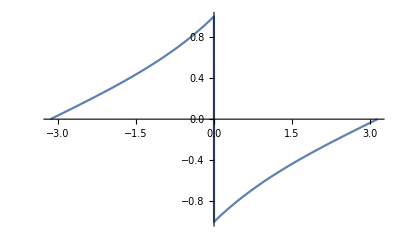

```mathematica
Plot[-(-1+√(2-2 Cos[py])+Cos[py]) Csc[py],{py,-π,π}]
```

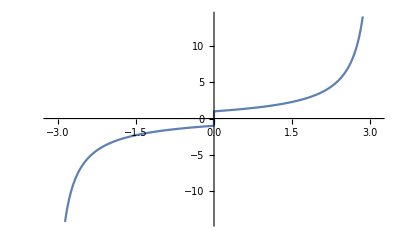

```mathematica
Plot[(1+√(2-2 Cos[py])-Cos[py]) Csc[py],{py,-π,π}]
```

```mathematica
FullSimplify[
Eigensystem[TheTransferM6[0,m]]
]
```

{{-2-m,2+m,-√(4+(-2+m) m),-√(4+(-2+m) m),√(4+(-2+m) m),√(4+(-2+m) m)},{{1,0,1,0,1,0},{0,1,0,1,0,1},{1/2 (1-m-√(4+(-2+m) m)),-1/2,1/2 (-1+m+√(4+(-2+m) m)),-1/2,0,1},{-1/2,1/2 (1-m+√(4+(-2+m) m)),-1/2,1/2 (-1+m-√(4+(-2+m) m)),1,0},{1/2 (1-m+√(4+(-2+m) m)),-1/2,1/2 (-1+m-√(4+(-2+m) m)),-1/2,0,1},{-1/2,1/2 (1-m-√(4+(-2+m) m)),-1/2,1/2 (-1+m+√(4+(-2+m) m)),1,0}}}

```mathematica
TheTransferM8[px_,m_]=({{2-m-2 Cos[px], 2 Sin[px], -1, -1, 0, 0, -1, 1}, {2 Sin[px], -2+m+2 Cos[px], 1, 1, 0, 0, -1, 1}, {-1, 1, 2-m-2 Cos[px], 2 Sin[px], -1, -1, 0, 0}, {-1, 1, 2 Sin[px], -2+m+2 Cos[px], 1, 1, 0, 0}, {0, 0, -1, 1, 2-m-2 Cos[px], 2 Sin[px], -1, -1}, {0, 0, -1, 1, 2 Sin[px], -2+m+2 Cos[px], 1, 1}, {-1, -1, 0, 0, -1, 1, 2-m-2 Cos[px], 2 Sin[px]}, {1, 1, 0, 0, -1, 1, 2 Sin[px], -2+m+2 Cos[px]}});
```

```mathematica
FullSimplify[Det[TheTransferM8[px,m]]]
```

(12+(-4+m) m+4 (-2+m) Cos[px])^2 (80+(-4+m) m (16+(-4+m) m)+8 (-2+m)^3 Cos[px]+8 (-4+m) m Cos[2 px])

```mathematica
Eigenvalues[TheTransferM8[px,m]]//MatrixForm
```

(-√(4+m^2+4 m Cos[px])
√(4+m^2+4 m Cos[px])
-√(20-8 m+m^2-16 Cos[px]+4 m Cos[px])
√(20-8 m+m^2-16 Cos[px]+4 m Cos[px])
-√(12-4 m+m^2-8 Cos[px]+4 m Cos[px])
-√(12-4 m+m^2-8 Cos[px]+4 m Cos[px])
√(12-4 m+m^2-8 Cos[px]+4 m Cos[px])
√(12-4 m+m^2-8 Cos[px]+4 m Cos[px]))

```mathematica
Manipulate[Plot[{√(4+m^2+4 m Cos[px]),-√(4+m^2+4 m Cos[px]),√(20-8 m+m^2-16 Cos[px]+4 m Cos[px]),-√(20-8 m+m^2-16 Cos[px]+4 m Cos[px]),√(12-4 m+m^2-8 Cos[px]+4 m Cos[px]),-√(12-4 m+m^2-8 Cos[px]+4 m Cos[px])},{px,-π,π}],{m,-10,10}]
```

```mathematica
A2=ⅈ*PauliMatrix[2]/2-PauliMatrix[3]/2//MatrixForm
```

(-1/2 | 1/2
-1/2 | 1/2)

```mathematica
B2[px_]:=2Sin[px]*PauliMatrix[1]/2-2Cos[px]PauliMatrix[3]/2+(2-m)PauliMatrix[3];
B2[px]//MatrixForm
```

(2-m-Cos[px] | Sin[px]
Sin[px] | -2+m+Cos[px])

```mathematica
CM2=-ⅈ*PauliMatrix[2]/2-PauliMatrix[3]/2//MatrixForm
```

(-1/2 | -1/2
1/2 | 1/2)

```mathematica
TheTransferM62[px_,m_]=({{2-m-Cos[px], Sin[px], -1/2, -1/2, -1/2, 1/2}, {Sin[px], -2+m+Cos[px], 1/2, 1/2, -1/2, 1/2}, {-1/2, 1/2, 2-m-Cos[px], Sin[px], -1/2, -1/2}, {-1/2, 1/2, Sin[px], -2+m+Cos[px], 1/2, 1/2}, {-1/2, -1/2, -1/2, 1/2, 2-m-Cos[px], Sin[px]}, {1/2, 1/2, -1/2, 1/2, Sin[px], -2+m+Cos[px]}});
```

```mathematica
FullSimplify[Det[TheTransferM62[px,m]]]
```

-(2+(-2+m) m+2 (-1+m) Cos[px]) (8+(-5+m) m+(-5+2 m) Cos[px])^2

```mathematica
Eigenvalues[TheTransferM62[px,m]]//MatrixForm
```

(-√(8-5 m+m^2-5 Cos[px]+2 m Cos[px])
-√(8-5 m+m^2-5 Cos[px]+2 m Cos[px])
√(8-5 m+m^2-5 Cos[px]+2 m Cos[px])
√(8-5 m+m^2-5 Cos[px]+2 m Cos[px])
-√(2-2 m+m^2-2 Cos[px]+2 m Cos[px])
√(2-2 m+m^2-2 Cos[px]+2 m Cos[px]))

```mathematica
Manipulate[
Plot[
{-√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),-√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),-√(2-2 m+m^2-2 Cos[px]+2 m Cos[px]),√(2-2 m+m^2-2 Cos[px]+2 m Cos[px])},
{px,-π,π}],
{m,-5,5}]
```

## Do it again in the Hamiltonian that I think is correct

```mathematica
A2=ⅈ*PauliMatrix[2]/2-PauliMatrix[3]/2//MatrixForm
```

(-1/2 | 1/2
-1/2 | 1/2)

```mathematica
B2[px_]:=2Sin[px]*PauliMatrix[1]/2-2Cos[px]PauliMatrix[3]/2+(2-m)PauliMatrix[3];
B2[px]//MatrixForm
```

(2-m-Cos[px] | Sin[px]
Sin[px] | -2+m+Cos[px])

```mathematica
CM2=-ⅈ*PauliMatrix[2]/2-PauliMatrix[3]/2//MatrixForm
```

(-1/2 | -1/2
1/2 | 1/2)

```mathematica
TheTransferM62[px_,m_]=({{2-m-Cos[px], Sin[px], -1/2, -1/2, -1/2, 1/2}, {Sin[px], -2+m+Cos[px], 1/2, 1/2, -1/2, 1/2}, {-1/2, 1/2, 2-m-Cos[px], Sin[px], -1/2, -1/2}, {-1/2, 1/2, Sin[px], -2+m+Cos[px], 1/2, 1/2}, {-1/2, -1/2, -1/2, 1/2, 2-m-Cos[px], Sin[px]}, {1/2, 1/2, -1/2, 1/2, Sin[px], -2+m+Cos[px]}});
```

```mathematica
FullSimplify[Det[TheTransferM62[px,m]]]
```

-(2+(-2+m) m+2 (-1+m) Cos[px]) (8+(-5+m) m+(-5+2 m) Cos[px])^2

```mathematica
Eigenvalues[TheTransferM62[px,m]]
```

{-√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),-√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),-√(2-2 m+m^2-2 Cos[px]+2 m Cos[px]),√(2-2 m+m^2-2 Cos[px]+2 m Cos[px])}

```mathematica
Manipulate[
Plot[
{-√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),-√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),√(8-5 m+m^2-5 Cos[px]+2 m Cos[px]),-√(2-2 m+m^2-2 Cos[px]+2 m Cos[px]),√(2-2 m+m^2-2 Cos[px]+2 m Cos[px])},
{px,-π,π},PlotLegends->"Placeholder"],
{m,-5,5}]
```

```mathematica
FullSimplify[Eigensystem[TheTransferM62[px,m]]]
```

{{-√(8+(-5+m) m+(-5+2 m) Cos[px]),-√(8+(-5+m) m+(-5+2 m) Cos[px]),√(8+(-5+m) m+(-5+2 m) Cos[px]),√(8+(-5+m) m+(-5+2 m) Cos[px]),-√(2+(-2+m) m+2 (-1+m) Cos[px]),√(2+(-2+m) m+2 (-1+m) Cos[px])},{{5/2-m-Cos[px]-√(8+(-5+m) m+(-5+2 m) Cos[px]),-1/2+Sin[px],-5/2+m+Cos[px]+√(8+(-5+m) m+(-5+2 m) Cos[px]),-1/2-Sin[px],0,1},{-1/2-Sin[px],5/2-m-Cos[px]+√(8+(-5+m) m+(-5+2 m) Cos[px]),-1/2+Sin[px],-5/2+m+Cos[px]-√(8+(-5+m) m+(-5+2 m) Cos[px]),1,0},{5/2-m-Cos[px]+√(8+(-5+m) m+(-5+2 m) Cos[px]),-1/2+Sin[px],-5/2+m+Cos[px]-√(8+(-5+m) m+(-5+2 m) Cos[px]),-1/2-Sin[px],0,1},{-1/2-Sin[px],5/2-m-Cos[px]-√(8+(-5+m) m+(-5+2 m) Cos[px]),-1/2+Sin[px],-5/2+m+Cos[px]+√(8+(-5+m) m+(-5+2 m) Cos[px]),1,0},{-(-1+m+Cos[px]+√(2+(-2+m) m+2 (-1+m) Cos[px])) Csc[px],1,-(-1+m+Cos[px]+√(2+(-2+m) m+2 (-1+m) Cos[px])) Csc[px],1,-(-1+m+Cos[px]+√(2+(-2+m) m+2 (-1+m) Cos[px])) Csc[px],1},{(1-m-Cos[px]+√(2+(-2+m) m+2 (-1+m) Cos[px])) Csc[px],1,(1-m-Cos[px]+√(2+(-2+m) m+2 (-1+m) Cos[px])) Csc[px],1,(1-m-Cos[px]+√(2+(-2+m) m+2 (-1+m) Cos[px])) Csc[px],1}}}